```mathematica
lw={};
For[x=-13.0,x≤ 10,x+=3;AppendTo[lw, {N[x],2x^2+3x-4}];]
MatrixForm[lw]
```

(-10. | 166.
-7. | 73.
-4. | 16.
-1. | -5.
2. | 10.
5. | 61.
8. | 148.
11. | 271.)

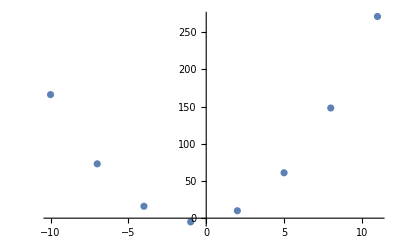

```mathematica
ListPlot[lw]
```

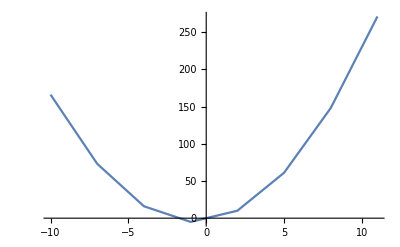

```mathematica
ListLinePlot[lw]
```

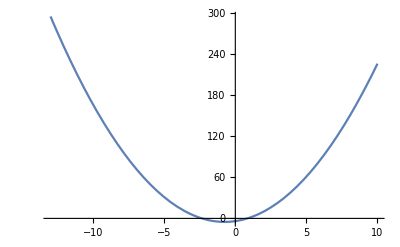

```mathematica
Plot[{2x^2+3x-4},{x,-13,10}]
```